テイラー（マクローリン）級数の収束

マクローリン級数の収束に関し次の例(教科書p.109,例題5.2)を用いて実験する。

関数の定義とマクローリン係数

```mathematica
f[x_]=E^x
```

ⅇ^x

```mathematica
F=Series[f[x],{x,0,6}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+O[x]^7

```mathematica
F=Normal[F]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720

グラフ

マクローリン級数の第n項までの和をg[n, x] とおく。

```mathematica
Do[g[n,x_]=Normal[Series[f[x],{x,0,n}]],{n,1,20}]
```

```mathematica
g[4,x]
```

1+x+x^2/2+x^3/6+x^4/24

```mathematica
gr[n_]:=Plot[g[n,x],{x,-4,4}]
```

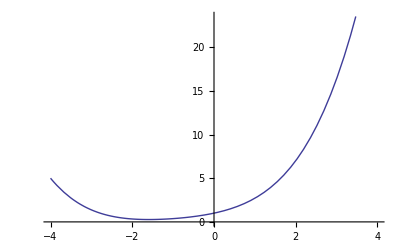

```mathematica
gr[4]
```

```mathematica
gr00:=Plot[f[x],{x,-4,4}]
```

アニメーションにして比較する。

```mathematica
Manipulate[Show[gr00,gr[n],AspectRatio->Automatic,PlotRange->{-4,4}],{n,0,6,1}]
```